```mathematica
Module[{h=24,timecount=0,v=0.3,bullets={},ufos={},cannons={},cannonballs={},cannonbroken={},explosions={},i=0,dst={},score=0,missing=0,broken=0,alive={{5,23},{7,23},{9,23}},gameover=False,tempdir={0,0}},ufo[p_]:=Polygon[{{-2,0},{0,-1},{2,0},{1,0},{0,0.5},{-1,0}}+Table[p,{6}]];
bullet[p_]:=Line[{p+{0,-0.5},p+{0,0.5}}];
craft[p_]:={Polygon[{{-1.5,0},{1.5,0},{0,0.9}}+Table[p,{3}]],Polygon[{{-0.5,0.5},{0.5,0.5},{0,2}}+Table[p,{3}]],Polygon[{{-1,-0.7},{1,-0.7},{0,0.5}}+Table[p,{3}]],Orange,Polygon[{{-0.4,-0.7},{0,-0.7},{-0.2,-1.5}}+Table[p,{3}]],Polygon[{{0.4,-0.7},{0,-0.7},{0.2,-1.5}}+Table[p,{3}]]};
cannon[p_,dir_]:={Gray,Rectangle[p+{-1,-1},p+{1,1},RoundingRadius->0.4],Black,Rotate[Rectangle[p+{-0.1,-0.2},p+{1.4,0.2}],Arg[dir[[1]]+dir[[2]] I],p]};
Manipulate[If[gameover,Goto[gover]];
explosions={};
timecount++;
If[0==Mod[timecount,4],AppendTo[bullets,u+{0,2}];
bullets=SortBy[bullets,Last];bullets=Reverse[bullets];
If[bullets[[1,2]]>25,bullets=Rest[bullets]]];
If[0==Mod[timecount,30],AppendTo[ufos,{RandomReal[{-8,8}],25}];
If[ufos[[1,2]]<-3,ufos=Rest[ufos];missing++;
If[4==missing,gameover=True]]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[ufos],dst=Table[Norm[ufos[[i]]-j],{j,bullets}];
If[Min[dst]≤1.5,AppendTo[explosions,ufos[[i]]];
ufos=Drop[ufos,{i}];score+=10,i++]]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[ufos],If[Norm[ufos[[i]]-u]≤2,AppendTo[explosions,ufos[[i]]];
ufos=Drop[ufos,{i}];score+=5;broken++;
alive=Rest[alive];If[3==broken,gameover=True],i++]]];
ufos+=Table[{0,-v},{Length[ufos]}];
bullets+=Table[{0,1},{Length[bullets]}];
If[score<100,Goto[gover]];
If[0==Mod[timecount,300],AppendTo[cannons,{RandomReal[{-8,8}],25}];
AppendTo[cannonbroken,0];
If[cannons[[1,2]]<-3,cannons=Rest[cannons];
cannonbroken=Rest[cannonbroken]]];
If[0==Mod[timecount,50],Do[If[i[[2]]>u[[2]],tempdir=(u-i)/Norm[u-i];
AppendTo[cannonballs,{i+tempdir*1.5,tempdir}]],{i,cannons}]];
If[0==Mod[timecount,50],i=1;
While[i≤Length[cannonballs],If[Norm[cannonballs[[i]][[1]]]>30,cannonballs=Drop[cannonballs,{i}],i++]]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[cannonballs],If[Norm[cannonballs[[i,1]]-u]≤2,cannonballs=Drop[cannonballs,{i}];broken++;
alive=Rest[alive];If[3==broken,gameover=True],i++]]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[cannons],If[Norm[cannons[[i]]-u]≤2,AppendTo[explosions,cannons[[i]]];cannons=Drop[cannons,{i}];
score+=20;broken++;alive=Rest[alive];
If[3==broken,gameover=True],i++]]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[cannons],dst=Table[Norm[cannons[[i]]-j],{j,bullets}];
If[Min[dst]≤1.5,cannonbroken[[i]]+=1];i++]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[cannons],If[5==cannonbroken[[i]],AppendTo[explosions,cannons[[i]]];
cannons=Drop[cannons,{i}];
cannonbroken=Drop[cannonbroken,{i}];score+=50,i++]]];
cannons+=Table[{0,-v/3},{Length[cannons]}];
cannonballs+=Table[{v*i[[2]],{0,0}},{i,cannonballs}];
Label[gover];
Graphics[If[!gameover,Join[Table[ufo[i],{i,ufos}],Table[bullet[i],{i,bullets}],Table[cannon[i,u-i],{i,cannons}],Table[Disk[i[[1]],0.2],{i,cannonballs}],Table[Circle[i,2],{i,explosions}],{craft[u],Text[Style[score,FontSize->24],{-8,23},Background->White],Red},Table[Disk[j,{0.5,0.3}],{j,alive}]],{Rectangle[{-10,-2},{10,24}],Text[Style[" Game over! ",FontSize->36],{0,16},Background->White],Text[Style[" Score: ",FontSize->24],{0,10},Background->White],Text[Style[score,FontSize->24],{0,7},Background->White]}],Axes->False,PlotRange->{{-10,10},{-2,24}}],{u,{-8.5,0},{8.5,22}},ControlPlacement->Right]]
```

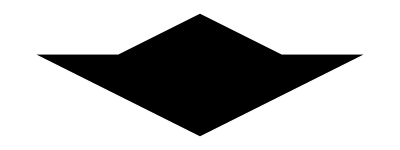

```mathematica
Graphics[ufo[{0,0}]]
```

```mathematica
ufo[p_]:=Polygon[{{-2,0},{0,-1},{2,0},{1,0},{0,0.5},{-1,0}}+Table[p,6]]
bullet[p_]:=Line[{p+{0,-0.5},p+{0,0.5}}]
craft[p_]:={Polygon[{{-1.5,0},{1.5,0},{0,0.9}}+Table[p,{3}]],Polygon[{{-0.5,0.5},{0.5,0.5},{0,2}}+Table[p,{3}]],Polygon[{{-1,-0.7},{1,-0.7},{0,0.5}}+Table[p,{3}]],Orange,Polygon[{{-0.4,-0.7},{0,-0.7},{-0.2,-1.5}}+Table[p,{3}]],Polygon[{{0.4,-0.7},{0,-0.7},{0.2,-1.5}}+Table[p,{3}]]}
cannon[p_,dir_]:={Gray,Rectangle[p+{-1,-1},p+{1,1},RoundingRadius->0.4],Black,Rotate[Rectangle[p+{-0.1,-0.2},p+{1.4,0.2}],Arg[dir⟦1⟧+dir⟦2⟧ I],p]}
```

```mathematica
Module[{h=24,timecount=0,v=0.3,bullets={},ufos={},cannons={},cannonballs={},cannonbroken={},explosions={},i=0,dst={},score=0,missing=0,broken=0,alive={{5,23},{7,23},{9,23}},gameover=False,tempdir={0,0}},
Manipulate[If[gameover,Goto[gover]];
explosions={};
timecount++;
If[0==Mod[timecount,4],AppendTo[bullets,u+{0,2}];
bullets=SortBy[bullets,Last];bullets=Reverse[bullets];
If[bullets[[1,2]]>25,bullets=Rest[bullets]]];
If[0==Mod[timecount,30],AppendTo[ufos,{RandomReal[{-8,8}],25}];
If[ufos[[1,2]]<-3,ufos=Rest[ufos];missing++;
If[4==missing,gameover=True]]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[ufos],dst=Table[Norm[ufos[[i]]-j],{j,bullets}];
If[Min[dst]≤1.5,AppendTo[explosions,ufos[[i]]];
ufos=Drop[ufos,{i}];score+=10,i++]]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[ufos],If[Norm[ufos[[i]]-u]≤2,AppendTo[explosions,ufos[[i]]];
ufos=Drop[ufos,{i}];score+=5;broken++;
alive=Rest[alive];If[3==broken,gameover=True],i++]]];
ufos+=Table[{0,-v},{Length[ufos]}];
bullets+=Table[{0,1},{Length[bullets]}];
If[score<100,Goto[gover]];
If[0==Mod[timecount,300],AppendTo[cannons,{RandomReal[{-8,8}],25}];
AppendTo[cannonbroken,0];
If[cannons[[1,2]]<-3,cannons=Rest[cannons];
cannonbroken=Rest[cannonbroken]]];
If[0==Mod[timecount,50],Do[If[i[[2]]>u[[2]],tempdir=(u-i)/Norm[u-i];
AppendTo[cannonballs,{i+tempdir*1.5,tempdir}]],{i,cannons}]];
If[0==Mod[timecount,50],i=1;
While[i≤Length[cannonballs],If[Norm[cannonballs[[i]][[1]]]>30,cannonballs=Drop[cannonballs,{i}],i++]]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[cannonballs],If[Norm[cannonballs[[i,1]]-u]≤2,cannonballs=Drop[cannonballs,{i}];broken++;
alive=Rest[alive];If[3==broken,gameover=True],i++]]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[cannons],If[Norm[cannons[[i]]-u]≤2,AppendTo[explosions,cannons[[i]]];cannons=Drop[cannons,{i}];
score+=20;broken++;alive=Rest[alive];
If[3==broken,gameover=True],i++]]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[cannons],dst=Table[Norm[cannons[[i]]-j],{j,bullets}];
If[Min[dst]≤1.5,cannonbroken[[i]]+=1];i++]];
If[0==Mod[timecount,5],i=1;
While[i≤Length[cannons],If[5==cannonbroken[[i]],AppendTo[explosions,cannons[[i]]];
cannons=Drop[cannons,{i}];
cannonbroken=Drop[cannonbroken,{i}];score+=50,i++]]];
cannons+=Table[{0,-v/3},{Length[cannons]}];
cannonballs+=Table[{v*i[[2]],{0,0}},{i,cannonballs}];
Label[gover];
Graphics[If[!gameover,Join[Table[ufo[i],{i,ufos}],Table[bullet[i],{i,bullets}],Table[cannon[i,u-i],{i,cannons}],Table[Disk[i[[1]],0.2],{i,cannonballs}],Table[Circle[i,2],{i,explosions}],{craft[u],Text[Style[score,FontSize->24],{-8,23},Background->White],Red},Table[Disk[j,{0.5,0.3}],{j,alive}]],{Rectangle[{-10,-2},{10,24}],Text[Style[" Game over! ",FontSize->36],{0,16},Background->White],Text[Style[" Score: ",FontSize->24],{0,10},Background->White],Text[Style[score,FontSize->24],{0,7},Background->White]}],Axes->False,PlotRange->{{-10,10},{-2,24}}],{u,{-8.5,0},{8.5,22}},ControlPlacement->Right]]
```